```mathematica
Dynamical System Equations
```

Dynamical Equations System

```mathematica
Equations to use:
```

```mathematica
ϕ=.
z=.
ξ=.
λ=.
f=.
v=.
g=.
e=.
Remove[f,v,g,e]
```

```mathematica
f[ϕ]=1+ξ*ϕ[N]^2;
f'[ϕ]=2ξ*ϕ[ N];
f''[ϕ]= 2ξ;
v[ϕ]=(λ/4)*ϕ[N]^4;
v'[ϕ]=λ*ϕ[N]^3;
g[ϕ]=(3ξ^2*ϕ[N]^2)/(1+ξ*ϕ[N]^2)(*0*);
g'[ϕ]=(6ξ^2*ϕ[N])/(1+ξ*ϕ[N]^2)^2(*0*);
e= 2*f[ϕ](1+g[ϕ])+3f'[ϕ]^2;
```

```mathematica
Eq1= z[N];
Eq2 = -(6f[ϕ]/e)*(f[ϕ]*(v'[ϕ]/v[ϕ])-2f'[ϕ])-
(3z[N]/e)*(3f[ϕ]*f'[ϕ]*(v'[ϕ]/v[ϕ])-3f'[ϕ]^2+2f[ϕ]*(1+g[ϕ]))+(z[N]^2/e)*(f[ϕ]*(v'[ϕ]/v[ϕ])*(1+g[ϕ])-f[ϕ]*g'[ϕ]-3f'[ϕ]^2*(v'[ϕ]/v[ϕ])-3f''[ϕ]*f'[ϕ]-7f'[ϕ]*(1+g[ϕ]))+(z[N]^3/(2*e))*(f'[ϕ]*(v'[ϕ]/v[ϕ])*(1+g[ϕ])-f'[ϕ]*g'[ϕ]+2*f''[ϕ]*(1+g[ϕ])+2(1+g[ϕ])^2);
```

```mathematica
ex = Eq1/.ϕ_[N]->ϕ;
ey= Eq2/.ϕ_[N]->ϕ;
boundary = 6f[ϕ]+6f'[ϕ]*z-(1+g[ϕ])*z^2 /. ϕ_[N]-> ϕ;
weff= -1 +(2f'[ϕ]/e)*(2f'[ϕ]-f[ϕ]*(v'[ϕ]/v[ϕ]))+(z*f'[ϕ]/e)*(-(8/3)*(1+g[ϕ])-2*f'[ϕ]*(v'[ϕ]/v[ϕ]))-(z^2/e)*(-(2/3)*(1+g[ϕ])^2+f'[ϕ]*g'[ϕ]/3-f'[ϕ]*(v'[ϕ]/(3v[ϕ]))*(1+g[ϕ])-(2/3)*f''[ϕ]*(1+g[ϕ])) /. ϕ_[N]-> ϕ;
```

Parameters

```mathematica
ξ=10^4;
λ=10^-3;
```

## Boundary of Physical Space

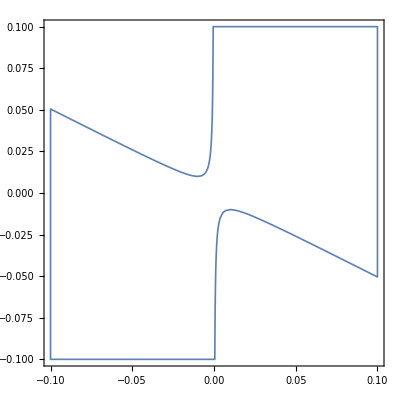

```mathematica
Boundary1=RegionPlot[boundary>0,{ϕ,-0.1,0.1},{z,-0.1,0.1},PlotStyle->None,BoundaryStyle->Thickness[0.003]]
```

## Accelerated, Superaccelerated, superstiff regions

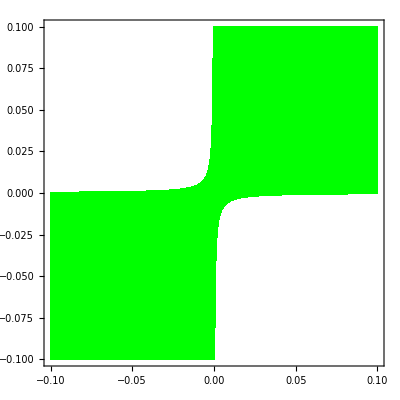

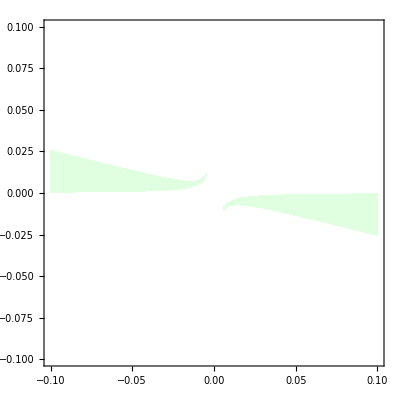

-Graphics-

```mathematica
superacc=RegionPlot[boundary>0 &&weff<-1,{ϕ,-0.1,0.1},{z,-0.1,0.1},PlotPoints->70,PlotStyle->Green,BoundaryStyle->None,Frame->True,Axes->False,RotateLabel->False,AspectRatio->Full]
acc=RegionPlot[boundary >0 &&-1<weff<-1/3,{ϕ,-0.1,0.1},{z,-0.1,0.1},PlotPoints->70,PlotStyle->{LightGreen},BoundaryStyle->None,Frame->True,Axes->False,RotateLabel->False,AspectRatio->Full]
superstiff=RegionPlot[boundary >0 &&weff>1,{ϕ,-0.1,0.1},{z,-0.1,0.1},PlotPoints->50,PlotStyle->{Yellow},BoundaryStyle->None,Frame->True,Axes->False,RotateLabel->False,AspectRatio->Full]
```

## NDSOLVE (Heteroclinic orbit )

{{ϕ→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

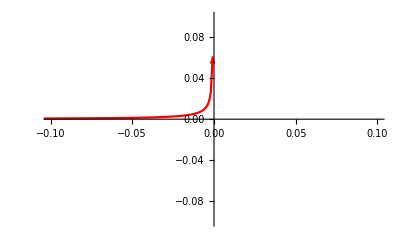

{{ϕ→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

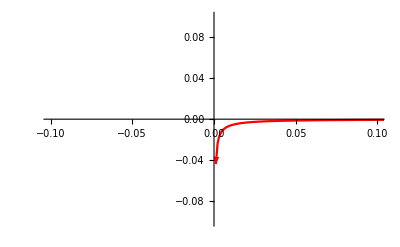

```mathematica
Sol=NDSolve[Evaluate[{{Eq1== ϕ'[N], Eq2== z'[N]},ϕ[0]==-0.11, z[0]==0.01}],{ϕ,z},{N,0,85.73}]
p1=ParametricPlot[Evaluate[{ϕ[N],z[N]}/.Sol],{N,0,85.73},PlotRange->{{-0.1,0.1},{-0.1,0.1}}, PlotStyle->{Red},AspectRatio->1/GoldenRatio]/. Line[x_]->{Arrowheads[{0,0.005,0.05,0.001,0}],Arrow[x]}
Sol2=NDSolve[Evaluate[{{Eq1== ϕ'[N], Eq2== z'[N]},ϕ[0]==0.11, z[0]==0.01}],{ϕ,z},{N,0,96.7}]
p2=ParametricPlot[Evaluate[{ϕ[N],z[N]}/.Sol2],{N,0,96.7},PlotRange->{{-0.1,0.1},{-0.1,0.1}}, PlotStyle->{Red},AspectRatio->1/GoldenRatio]/.Line[x_]->{Arrowheads[{0,0.005,0.05,0.001,0}],Arrow[x]}
```

## Stream Plot

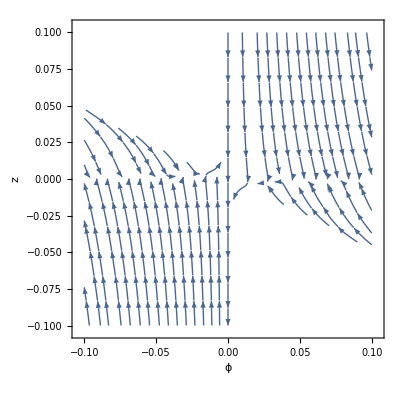

```mathematica
st=StreamPlot[{ex,ey},{ϕ,-0.1,0.1},{z,-0.1,0.1},RegionFunction->Function[{ϕ,z},boundary>0],AspectRatio->Full,FrameLabel->{ϕ,z},RotateLabel->False,Frame->True]
```

## Final Figure

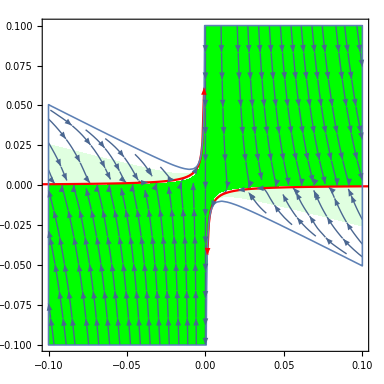

```mathematica
Show[superacc,acc,superstiff,st,p1,p2,Boundary1, PlotRange->{{-0.1,0.1},{-0.1,0.1}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["QuarticPotentialPalatiniEta10_7.pdf",Show[superacc,acc,superstiff,st,p1,p2,Boundary1, PlotRange->{{-0.005,0.005},{-0.005,0.005}}]]
```

QuarticPotentialPalatiniEta10_7.pdf